```mathematica
Clear[tpara,tperp,rpara,rperp,ni,nt]
```

```mathematica
tpara[θi_]:=(2ni Cos[θi])/(ni Cos[θt[θi]]+nt Cos[θi])
```

```mathematica
tperp[θi_]:=(2ni Cos[θi])/(ni Cos[θi]+nt Cos[θt[θi]])
```

```mathematica
rperp[θi_]:=(ni Cos[θi]-nt Cos[θt[θi]])/(ni Cos[θi]+nt Cos[θt[θi]])
```

```mathematica
rpara[θi_]:=(ni Cos[θt[θi]]-nt Cos[θi])/(ni Cos[θt[θi]]+nt Cos[θi])
```

```mathematica
θt[θi_]:=ArcSin[ni/nt Sin[θi]]
```

```mathematica
(*Air-to-Glass*)
```

```mathematica
ni=1.;nt=1.5;
```

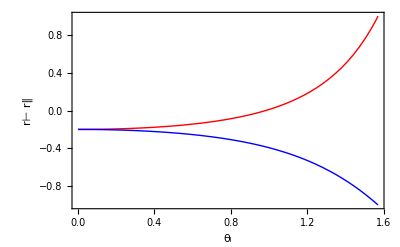

```mathematica
Plot[{rpara[θi],rperp[θi]},{θi,0,π/2},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{Subscript[θ, i],"r⊢   r‖"}]
```

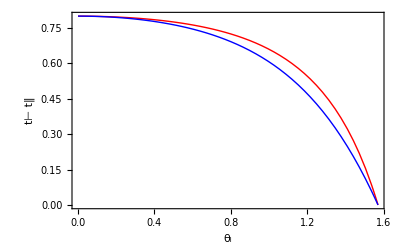

```mathematica
Plot[{tpara[θi],tperp[θi]},{θi,0,π/2},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{Subscript[θ, i],"t⊢   t‖"}]
```

```mathematica
(*Attention : on n'a PAS r+t=1 ni r^2+t^2=1 mais R+T=1*)
```

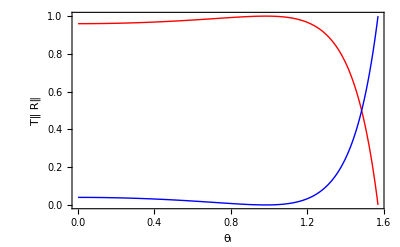

```mathematica
Plot[{tpara[θi]^2(nt Cos[θt[θi]])/(ni Cos[θi]),rpara[θi]^2},{θi,0,π/2},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{Subscript[θ, i],"T‖   R‖"}]
```

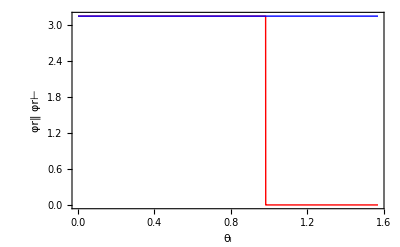

```mathematica
Plot[{Arg[rpara[θi]],Arg[rperp[θi]]},{θi,0,π/2},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{Subscript[θ, i],"φr‖    φr⊢"}]
```

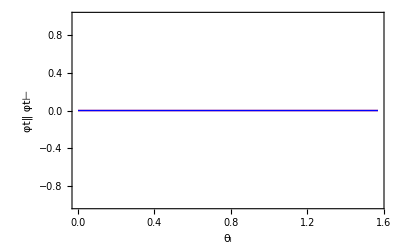

```mathematica
Plot[{Arg[tpara[θi]],Arg[tperp[θi]]},{θi,0,π/2},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{Subscript[θ, i],"φt‖    φt⊢"}]
```

```mathematica
(*Glass-to-Air*)
```

```mathematica
Clear[tpara,tperp,rpara,rperp,ni,nt]
```

```mathematica
tpara[θi_]:=(2ni Cos[θi])/(ni Cos[θt[θi]]+nt Cos[θi])
```

```mathematica
tperp[θi_]:=(2ni Cos[θi])/(ni Cos[θi]+nt Cos[θt[θi]])
```

```mathematica
rperp[θi_]:=(ni Cos[θi]-nt Cos[θt[θi]])/(ni Cos[θi]+nt Cos[θt[θi]])
```

```mathematica
rpara[θi_]:=(ni Cos[θt[θi]]-nt Cos[θi])/(ni Cos[θt[θi]]+nt Cos[θi])
```

```mathematica
θt[θi_]:=ArcSin[ni/nt Sin[θi]]
```

```mathematica
ni=1.5;nt=1.;
```

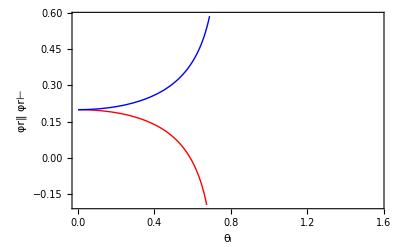

```mathematica
Plot[{rpara[θi],rperp[θi]},{θi,0,π/2},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{Subscript[θ, i],"φr‖    φr⊢"}]
```

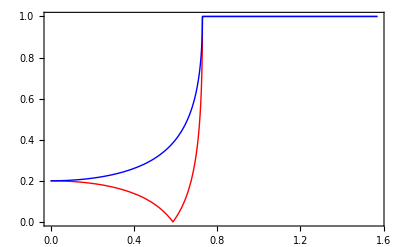

```mathematica
Plot[{Abs[rpara[θi]],Abs[rperp[θi]]},{θi,0,π/2},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True]
```

```mathematica
Abs[rpara[0.735]]
```

1.

```mathematica
(*Ici tpara et tperp ne sont pas définis : onde évanescente*)
```

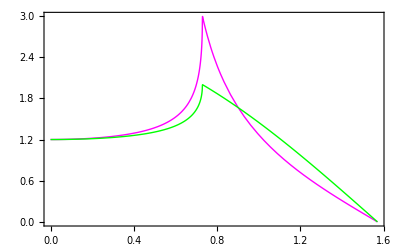

```mathematica
Plot[{Abs[tpara[θi]],Abs[tperp[θi]]},{θi,0,π/2},PlotStyle->{{Magenta,Thick},{Green,Thick}},Frame->True]
```

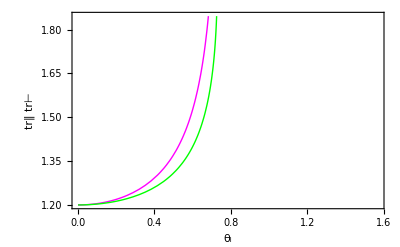

```mathematica
Plot[{tpara[θi],tperp[θi]},{θi,0,π/2},PlotStyle->{{Magenta,Thick},{Green,Thick}},Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{Subscript[θ, i],"tr‖    tr⊢"}]
```

```mathematica
(*Attention : on n'a PAS r+t=1 ni r^2+t^2=1 mais R+T=1*)
```

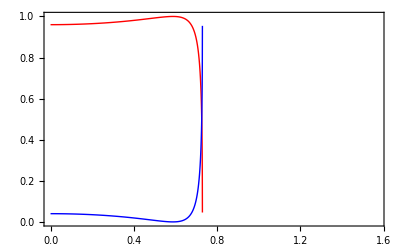

```mathematica
Plot[{tpara[θi]^2(nt Cos[θt[θi]])/(ni Cos[θi]),rpara[θi]^2},{θi,0,π/2},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True]
```

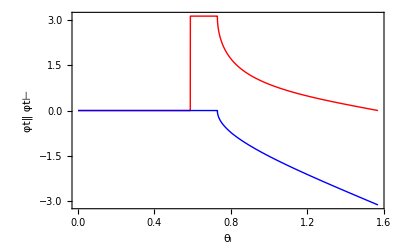

```mathematica
Plot[{Arg[rpara[θi]],Arg[rperp[θi]]},{θi,0,π/2},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{Subscript[θ, i],"φt‖    φt⊢"}]
```

```mathematica
{Arg[rpara[π/4]],Arg[rperp[π/4]]}
```

{1.85459,-0.643501}

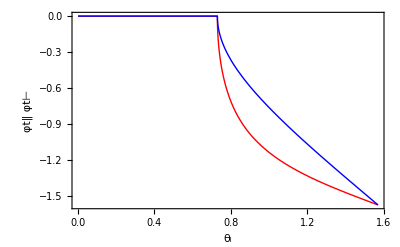

```mathematica
Plot[{Arg[tpara[θi]],Arg[tperp[θi]]},{θi,0,π/2},PlotStyle->{{Red,Thick},{Blue,Thick}},Frame->True,LabelStyle->{Bold,Directive[14]},FrameLabel->{Subscript[θ, i],"φt‖    φt⊢"}]
```

```mathematica
{Arg[tpara[π/4]],Arg[tperp[π/4]]}
```

{-0.643501,-0.321751}

```mathematica
{ArcSin[1/1.5],ArcTan[1/1.5]}
```

{0.729728,0.588003}

```mathematica
{ArcSin[1/1.4],ArcTan[1/1.4]}
```

{0.795603,0.620249}

```mathematica
√2
```

√2

```mathematica
Lame[β_,δ_]:={{ⅇ^(ⅈ δ/2)Cos[β]^2+ⅇ^(-ⅈ δ/2)Sin[β]^2,ⅈ Sin[2β]Sin[δ/2]},{ⅈ Sin[2β]Sin[δ/2],ⅇ^(-ⅈ δ/2)Cos[β]^2+ⅇ^(ⅈ δ/2)Sin[β]^2}}
```

```mathematica
Lame[β,π]
```

{{ⅈ Cos[β]^2-ⅈ Sin[β]^2,ⅈ Sin[2 β]},{ⅈ Sin[2 β],-ⅈ Cos[β]^2+ⅈ Sin[β]^2}}

```mathematica
Lame[β,π/2]//ExpToTrig//Simplify
```

{{(1+ⅈ Cos[2 β])/(√2),ⅈ √2 Cos[β] Sin[β]},{ⅈ √2 Cos[β] Sin[β],(1-ⅈ Cos[2 β])/(√2)}}

```mathematica
Lame[0,δ]
```

{{ⅇ^((ⅈ δ)/2),0},{0,ⅇ^(-(ⅈ δ)/2)}}

```mathematica
Lame[π/4,π/2]
```

{{1/2 ⅇ^(-(ⅈ π)/4)+1/2 ⅇ^((ⅈ π)/4),ⅈ/(√2)},{ⅈ/(√2),1/2 ⅇ^(-(ⅈ π)/4)+1/2 ⅇ^((ⅈ π)/4)}}

```mathematica
Lame[π/8,π]
```

{{ⅈ Cos[π/8]^2-ⅈ Sin[π/8]^2,ⅈ/(√2)},{ⅈ/(√2),-ⅈ Cos[π/8]^2+ⅈ Sin[π/8]^2}}

```mathematica
Lame[π/4,π]
```

{{0,ⅈ},{ⅈ,0}}

```mathematica
Lame[β0,π/2].Lame[β1,π].Lame[β2,π/2]//MatrixForm//Simplify
```

(1/2 (-Cos[2 (β0-β1)]+ⅈ (Cos[2 β1]+ⅈ Cos[2 (β1-β2)]-Cos[2 (β0-β1+β2)])) | 1/2 (Sin[2 (β0-β1)]+ⅈ Sin[2 β1]+Sin[2 (β1-β2)]-ⅈ Sin[2 (β0-β1+β2)])
1/2 (-Sin[2 (β0-β1)]+ⅈ (Sin[2 β1]+ⅈ Sin[2 (β1-β2)]-Sin[2 (β0-β1+β2)])) | 1/2 ⅈ (ⅈ Cos[2 (β0-β1)]-Cos[2 β1]+ⅈ Cos[2 (β1-β2)]+Cos[2 (β0-β1+β2)]))

```mathematica
Lame[β0,π/2].Lame[β1,π].Lame[β2,π/2].{1,0}//MatrixForm//Simplify
```

(1/2 (-Cos[2 (β0-β1)]+ⅈ (Cos[2 β1]+ⅈ Cos[2 (β1-β2)]-Cos[2 (β0-β1+β2)]))
1/2 (-Sin[2 (β0-β1)]+ⅈ (Sin[2 β1]+ⅈ Sin[2 (β1-β2)]-Sin[2 (β0-β1+β2)])))

```mathematica
v=Lame[β0,π/2].Lame[β1,π].Lame[β2,π/2].{1,0}//Simplify
```

{1/2 (-Cos[2 (β0-β1)]+ⅈ (Cos[2 β1]+ⅈ Cos[2 (β1-β2)]-Cos[2 (β0-β1+β2)])),1/2 (-Sin[2 (β0-β1)]+ⅈ (Sin[2 β1]+ⅈ Sin[2 (β1-β2)]-Sin[2 (β0-β1+β2)]))}

```mathematica
ComplexExpand[v.Conjugate[v]]//Simplify
```

1